# In-Class Demo (01-20-2022)

## Bifurcation Diagrams

Let’s consider the following model for the number of fish living in a pond that is subjected to fishing.  This situation is modeled by the differential equation 
x' = x^3-k x
where k is a real-valued constant (in this case, we will let k take on negative numbers as well).

First, let’s write the differential equation in the form x' = f(x) .  We will also define a function called fPrime that will be used later in the linearization of the ODE.  Here, fPrime is simply given by the following calculation.

```mathematica
f[x_,k_] = x^3-k x
fPrime[x_,k_]=D[f[x,k],x]
```

-k x+x^3

-k+3 x^2

Now, let’s find the equilibrium points as a function of the parameter q so that we can visualize them on plots.  We can do this using the Solve command in Mathematica as follows:

```mathematica
eqPts[k_]=Solve[f[x,k]==0,x]
```

{{x→0},{x→-√k},{x→√k}}

```mathematica
kVals = Table[k,{k,-2,2,.1}];
animateImages = kVals;
For[j=1,j≤Length[kVals],j++,
p1 = Plot[f[x,kVals[[j]]],{x,-2,2}]; 
p2 = ListPlot[{x,0}/.eqPts[kVals[[j]]],PlotStyle->{Red,PointSize[Large]}]; 
animateImages[[j]]=Show[p1,p2, PlotRange->{{-2,2},{-1,1}},AxesLabel->{x,x'}]];
rasterizedFrames=Map[Image,animateImages];
ListAnimate[rasterizedFrames]
```

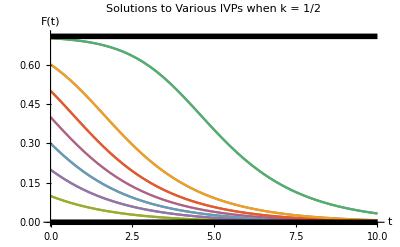

```mathematica
sol[α_,q_] := Quiet[DSolve[{D[x[t],t]==f[x[t],q],x[0] == α},x[t],t]];
p3 = Quiet[Plot[Evaluate[Table[x[t]/.sol[α,1/2],{α,0,1,.1}]],{t,0,10},
PlotLabel->"Solutions to Various IVPs when k = 1/2",
AxesLabel->{"t","x(t)"}]];
p4 =Plot[x/.eqPts[1/2],{t,0,10},
PlotStyle->{{Black,Thickness[.01]}}] ;
Show[p3,p4,
AxesLabel->{t,F[t]}]
```

```mathematica
BifurcationPlot[eqpts_,fPrime_,varrange_,plotCommands_]:=Module[{plotStable,plotUnstable,condition},
For[j=1,j≤Length[eqpts],j++,
condition=Simplify[(fPrime/.eqpts[[j]])]<0;
Subscript[plotStable, j] = Plot[If[condition,Evaluate[eqpts[[j,1,2]]]],varrange,PlotStyle->{Black,Thick}];
Subscript[plotUnstable, j]=Plot[If[Not[condition],Evaluate[eqpts[[j,1,2]]]],varrange,PlotStyle->{Red,Thick,Dashed}]];
Show[Table[{Subscript[plotStable, j],Subscript[plotUnstable, j]},{j,1,Length[eqpts]}],PlotRange->All,plotCommands]]
```

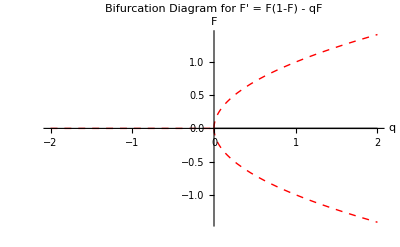

```mathematica
p5 = BifurcationPlot[eqPts[k],fPrime[x,k],{k,-2,2},
{
PlotLabel->"Bifurcation Diagram for F' = F(1-F) - qF",
AxesLabel->{"q","F"}
}]
```

What the above figure allows us to see is just how the phase line changes as the parameters change.  The following block of code is solely meant for you to be able to visualize what is going on all at the same time.  You don’t need to know how to code the following.  Just simply run it and watch the resulting images.  

Warning: the following block of code take a little while to run.

```mathematica
p5 = BifurcationPlot[eqPts[k],fPrime[x,k],{k,-2,2},
{
PlotLabel->"Bifurcation Diagram for x' = x^3 - k x",
AxesLabel->{"k","x"}
}];

kVals = Table[kk,{kk,-1,1,.2}];
animateImages=kVals;
For[j=1,j≤Length[animateImages],j++,
qq=kVals[[j]];

p6 = ListPlot[{qq,x}/.eqPts[qq],
PlotStyle->{Black,PointSize[Large]}];
P5=Show[p5,p6,
PlotRange->{-1.5,1.5}];
p1 = Plot[f[x,qq],{x,-2,2}]; 
p2 = ListPlot[{x,0}/.eqPts[qq],PlotStyle->{Black,PointSize[Large]}]; 
P1 = Show[p1,p2, 
AxesLabel->{x,x'},
PlotLabel->"x' vs x when k = "<>ToString[qq]];
p3 = Quiet[Plot[Evaluate[Table[x[t]/.sol[α,qq],{α,-.2,1,.1}]],{t,0,10},
PlotRange->{-1.5,1.5}]];
p4 =Plot[x/.eqPts[qq],{t,0,10},
PlotStyle->{{Black,Thickness[.01]}}] ;
P2 = Show[p3,p4,
AxesLabel->{t,x[t]},
PlotLabel->"Solutions to Various IVPs when k = "<>ToString[qq],
AxesLabel->{"t","x(t)"},
PlotRange->{-1.5,1.5}];
animateImages[[j]]=GraphicsGrid[{{P1,P5,P2}},ImageSize->Full]];
rasterizedFrames=Map[Image,animateImages];
ListAnimate[rasterizedFrames,ImageSize->Full]
```

$Aborted

Image::imgarray: The specified argument -2. should be an array of rank 2 or 3 with machine-sized numbers.

Image::imgarray: The specified argument -1.5 should be an array of rank 2 or 3 with machine-sized numbers.

Image::imgarray: The specified argument -1. should be an array of rank 2 or 3 with machine-sized numbers.

General::stop: Further output of Image::imgarray will be suppressed during this calculation.